```mathematica
Remove["Global`*"]
```

```mathematica
Share[]
```

8210848

Set your directory to where the MSTM output files are written

```mathematica
SetDirectory["C:\\Users\\mackodw\\Documents\\for\\msscat\\tm-2010\\mstm january 2022"]
```

C:\Users\mackodw\Documents\for\msscat\tm-2010\mstm january 2022

Execute the following module definitions: these are used for processing the output files.

```mathematica
nfread[file_]:=Module[{f,dat,sdat,pos,n,c,cdim,tdat,gmin,gmax,nb,bdat},f=OpenRead[file];
tdat={};
Do[
pos=Find[f," run number"];
If[ToString[pos]=="EndOfFile",Break[]];
n=Read[f,Number];
n=Read[f,Number];
If[n>0,c=ReadList[f,Table[Number,{4}],n],c={}];
sdat={n,c};
n=Read[f,Number];
If[n>0,c=ReadList[f,Number,n],c={}];
bdat={n,c};
gmin=Read[f,Table[Number,{3}]];
gmax=Read[f,Table[Number,{3}]];
cdim=Read[f,Table[Number,{3}]];
n=cdim[[1]]cdim[[2]]cdim[[3]];
dat=ReadList[f,Table[Number,{27}],n];
tdat=Append[tdat,{cdim,{gmin,gmax},sdat,bdat,dat}];
,{i,1,1000}];
Close[f];
tdat]
cplot[tdat_]:=Module[{cdim,rmin,rmax,splot,nb,bplot,ep,b,arat},
cdim=tdat[[1]];
p=Which[cdim[[1]]==1,1,cdim[[2]]==1,2,cdim[[3]]==1,3];
rmin=Drop[tdat[[2,1]],{p}];rmax=Drop[tdat[[2,2]],{p}];
ppos=tdat[[2,1,p]];
ns=tdat[[3,1]];sdat=tdat[[3,2]];
nis=0;ispos={};israd={};
Do[
t1=Abs[sdat[[i,p]]-ppos];
If[t1<sdat[[i,4]],
nis=nis+1;
ispos=Append[ispos,Drop[sdat[[i,{1,2,3}]],{p}]];
israd=Append[israd,Sqrt[sdat[[i,4]]^2-t1^2]];
];
,
{i,1,ns}];
splot=Table[Circle[ispos[[i]],israd[[i]]],{i,1,nis}];
nb=tdat[[4 ,1]];b=tdat[[4,2]];
bplot=If[nb>0,Table[Line[{{rmin[[1]],b[[i]]},{rmax[[1]],b[[i]]}}],{i,1,nb}],{}];
ep=Epilog->{splot,bplot};
arat=AspectRatio->Which[p==1,cdim[[3]]/cdim[[2]],p==2,cdim[[3]]/cdim[[1]],p==3,cdim[[2]]/cdim[[1]]];
{ep,arat}]
readmstm[file_,vars_,len_]:=Module[{f,newlist,str,dat,pos,tdat,t1},
f=OpenRead[file];
newlist=" input variables";
str=Find[f,newlist];
dat={};
Do[
pos=StreamPosition[f];
tdat=Table[Null[],{Length[vars]}];
Do[
str=ToString[Find[f,{newlist,vars[[j]]}]];
If[str==ToString[EndOfFile],Break[]];
If[Length[StringCases[str,vars[[j]]]]!=0,
t1=Read[f,Table[Number,{len[[j]]}]][[len[[j]]]];
tdat[[j]]=t1;
];
SetStreamPosition[f,pos];
,{j,1,Length[vars]}];
dat=Append[dat,tdat];
str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
,{i,1,100000}];
Close[f];
dat]
```

```mathematica
ndat=nfread["nf-fig1.dat"];
{ep,arat}=cplot[ndat[[1]]];
pdat=ndat[[1,-1]];
```

```mathematica
pl={12,18,22,26};
```

```mathematica
g=Table[ListContourPlot[pdat[[All,{1,3,pl[[i]]}]],PlotRange->All,PlotRangePadding->None,ep,arat,Contours->20,ColorFunction->"Rainbow"],{i,1,Length[pl]}];
```

```mathematica
g2=GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]],g[[4]]}},ImageSize->Large]
```

-Graphics-

```mathematica
vars={"   sphere    host"," down and up hemis"," down and up hemis"," waveguide"};
len={7,1,2,1};
dat=readmstm["mstm-2022b-fig2.dat",vars,len];
```

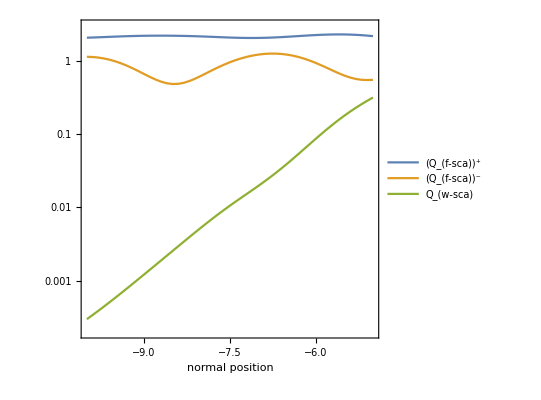

```mathematica
g=ListLogPlot[{dat[[All,{1,3}]],dat[[All,{1,2}]],dat[[All,{1,4}]]},Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{" normal position",""},PlotLegends->Placed[{"(Q_(f-sca))^+","(Q_(f-sca))^-", "Q_(w-sca)"},{.4,.6}],PlotRangePadding->None,PlotRange->{.0002,3}]
```

```mathematica
ndat=nfread["nf-fig3a.dat"];
{ep,arat}=cplot[ndat[[1]]];
pdat1=ndat[[1,-1]];
```

```mathematica
g1=ListContourPlot[pdat1[[All,{1,3,18}]],PlotRange->All,PlotRangePadding->None,ep,arat,Contours->20,ColorFunction->"Rainbow"];
```

```mathematica
ndat=nfread["nf-fig3b.dat"];
{ep,arat}=cplot[ndat[[1]]];
pdat1=ndat[[1,-1]];
```

```mathematica
g2=ListContourPlot[pdat1[[All,{1,3,18}]],PlotRange->All,PlotRangePadding->None,ep,arat,Contours->20,ColorFunction->"Rainbow"];
```

```mathematica
g3=GraphicsGrid[{{g1,g2}},ImageSize->Large]
```

-Graphics-

```mathematica
ndat=nfread["nf-fig4.dat"];
{ep,arat}=cplot[ndat[[1]]];
pdat=ndat[[1,-1]];
```

```mathematica
pl={12,18,22,26};
```

```mathematica
g=Table[ListContourPlot[pdat[[All,{1,3,pl[[i]]}]],PlotRange->All,PlotRangePadding->None,ep,arat,Contours->20,ColorFunction->"Rainbow"],{i,1,Length[pl]}];
```

```mathematica
g2=GraphicsGrid[{{g[[1]],g[[2]],g[[3]],g[[4]]}},ImageSize->Large]
```

-Graphics-

```mathematica
vars={" incident alpha"," unit cell reflectance"," unit cell reflectance"};
len={2,4,7};
dat=readmstm["mstm-2022b-fig5.dat",vars,len];
```

```mathematica
ListLogPlot[{dat[[All,{1,2}]],dat[[All,{1,3}]]},Joined->True,PlotStyle->{Blue,Red},Frame->True,PlotRangePadding->None,FrameStyle->Medium,FrameLabel->{"incident angle, deg"},PlotLegends->Placed[{"parallel","perpendicular"},{.7,.3}],AspectRatio->1,PlotRange->{.001,1}]
```

-Graphics-